```mathematica
A[t_, δ_] := Cos[g*δ]*PauliMatrix[4] - ⅈ*Sin[g*δ]*PauliMatrix[1];
B[t_, δ_]:= Cos[ B*Cos[ω*t]*δ]*PauliMatrix[4] - ⅈ*Sin[ B*Cos[ω*t]*δ]*PauliMatrix[3];
g=1;
Trotter[n_, T_, ω_] := Module[{},
rtn = PauliMatrix[4];
δ = T/(2*n);
For[i=0, i < n, i++, 
rtn = rtn.A[i*δ, δ].B[i*δ, δ]];
rtn.{{1/Sqrt[2]}, {1/Sqrt[2]}}]

maxω = 20
numsamples = 100
width = maxω/numsamples
ωs = maxω *Range[numsamples]/numsamples
maxt = .01
numsamples = 5
times = maxt*Range[numsamples]/numsamples

data =Table[ParallelTable[Norm[ND[Needs["NumericalCalculus`"];Trotter[10, t, ω], B, 0][[1]][[1]]]^2,{t, times}], {ω, ωs}];
```

20

100

1/5

{1/5,2/5,3/5,4/5,1,6/5,7/5,8/5,9/5,2,11/5,12/5,13/5,14/5,3,16/5,17/5,18/5,19/5,4,21/5,22/5,23/5,24/5,5,26/5,27/5,28/5,29/5,6,31/5,32/5,33/5,34/5,7,36/5,37/5,38/5,39/5,8,41/5,42/5,43/5,44/5,9,46/5,47/5,48/5,49/5,10,51/5,52/5,53/5,54/5,11,56/5,57/5,58/5,59/5,12,61/5,62/5,63/5,64/5,13,66/5,67/5,68/5,69/5,14,71/5,72/5,73/5,74/5,15,76/5,77/5,78/5,79/5,16,81/5,82/5,83/5,84/5,17,86/5,87/5,88/5,89/5,18,91/5,92/5,93/5,94/5,19,96/5,97/5,98/5,99/5,20}

0.01

5

{0.002,0.004,0.006,0.008,0.01}

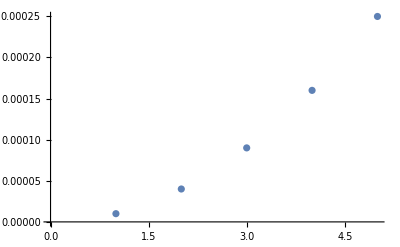

```mathematica
(*B = g = 1*)
ListPlot[Total[data]*width]
```